# Крестики-нолики

#### Бейзеров Максим Бочкарев Иван Трухан Елизавета

## Графическая часть (вид крестиков - ноликов)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nolik=
Graphics[{Thickness[0.05],Lighter[Orange,.4],Circle[]}];
krestik=
Graphics[{Thickness[0.05],Lighter[Blue,.4],Line[{{0.5,0.5},{-0.5,-0.5}}],Line[{{-0.5,0.5},{0.5,-0.5}}]}];
```

```mathematica
Manipulate[FromCharacterCode[X,"Unicode"],{X,0,200000,1}]
```

```mathematica
Graphics[Text[Style[FromCharacterCode[137317],50]],ImageSize->50]
```

-Graphics-

```mathematica
nolik=%
```

-Graphics-

```mathematica
color=ColorSlider[Dynamic[color]]
```

$CellContext`color

```mathematica
color
```

```mathematica
Dynamic[color]
```

```mathematica
Manipulate[{Graphics[{Text[Style[FromCharacterCode[X,"Unicode"],color,50]]}],Grid[{{Button["ToKrestik",Set[krestik,Graphics[Text[Style[FromCharacterCode[X,"Unicode"],color,50]],ImageSize->50]]]},{Button["ToNolik",Set[nolik,Graphics[Text[Style[FromCharacterCode[X,"Unicode"],color,50]],ImageSize->50]]]}



}]},{X,0,200000,1},{Color,ColorSlider[Dynamic[color]]}]
```

```mathematica
Manipulate[{Graphics[{Text[Style[FromCharacterCode[X,"Unicode"],color,50]]}],Grid[{{Button["ToKrestik",Set[krestik,Graphics[Text[Style[FromCharacterCode[X,"Unicode"],color,50]],ImageSize->50]]]}{Button["ToNolik",Set[nolik,Graphics[Text[Style[FromCharacterCode[X,"Unicode"],color,50]],ImageSize->50]]]},
{Button["ImportToKrestik",CreateDialog[{TextCell["Enter a name: "],InputField[Dynamic[nm],String],DefaultButton[DialogReturn[ret=nm];krestik=Import[ret,ImageSize->50]]}];]}
{Button["ImportToNolik",CreateDialog[{TextCell["Enter a name: "],InputField[Dynamic[nm],String],DefaultButton[DialogReturn[ret=nm];nolik=Import[ret,ImageSize->50]]}];]}

}]},{X,0,200000,1},{Color,ColorSlider[Dynamic[color]]}]
```

```mathematica
{krestik,nolik}
```

{-Graphics-,-Graphics-}

```mathematica
krestik
```

-Graphics-

```mathematica
Import[]
```

```mathematica
CreateDialog[{TextCell["Enter a name: "],InputField[Dynamic[nm],String],DefaultButton[DialogReturn[ret=nm]]}];
```

```mathematica
ret
Import[ret]
```

C:\Users\USER\Downloads\maxresdefault.jpg

-Graphics-

```mathematica
a
```

{{InfiniteLine[{-1.5,0.5},{0,1}],InfiniteLine[{-0.5,0.5},{0,1}],InfiniteLine[{0.5,0.5},{0,1}],InfiniteLine[{1.5,0.5},{0,1}],InfiniteLine[{2.5,0.5},{0,1}]},{InfiniteLine[{0.5,-1.5},{1,0}],InfiniteLine[{0.5,-0.5},{1,0}],InfiniteLine[{0.5,0.5},{1,0}],InfiniteLine[{0.5,1.5},{1,0}],InfiniteLine[{0.5,2.5},{1,0}]}}

## Бесконечное поле с самим собой

```mathematica
center = {{0,0},{0,0}};
width = {{-2,2}, {-2,2}};
range = center + scale *width;
scale = 1;
DynamicModule[{scalelist = {} ,delta = 0.,speed = 1,draglist = {},dx = 0, dy = 0,kr = {}, nol = {} ,currentMove = True,minlimx = -4, maxlimx =4,minlimy = -4, maxlimy =4},
EventHandler[Dynamic@Graphics[{LightGray,Rectangle[Round[MousePosition["Graphics"]/. None -> (scale*range[[All,2]] + 2)]-{0.5,0.5}],Darker[Gray], Thick, a ={InfiniteLine[{#+0.5,0.5}, {0,1}]& /@ Range[minlimx,maxlimx],InfiniteLine[{0.5,#+0.5}, {1,0}]& /@ Range[minlimy,maxlimy]},kr, nol},PlotRange-> (center+scale*width), Background-> White], { "MouseClicked":>(If[!ContainsAny[Join[kr,nol][[All,2]],{Round[MousePosition["Graphics"]]}],If[currentMove,AppendTo[kr,Inset[krestik,Round[MousePosition["Graphics"]],{0,0}, {0.7,0.7}]]; currentMove = !currentMove ,AppendTo[nol,Inset[nolik,Round[MousePosition["Graphics"]], {0,0}, {0.7,0.7}]]; currentMove = !currentMove] ]),"MouseDragged" :> (AppendTo[draglist, MousePosition["Graphics"]]; {dx,dy} = draglist[[-1]]-draglist[[1]];center-={{dx,dx}, {dy,dy}}/scale),
"MouseUp" :> (draglist={};
{{minlimx, maxlimx}, {minlimy, maxlimy}} = Round[center]+ Ceiling[scale*width]), 
{"MouseUp",2} :> (scalelist={};{{minlimx, maxlimx}, {minlimy, maxlimy}} = Round[center]+ Ceiling[scale*width]),{"MouseDragged",2} :> (AppendTo[scalelist, -1+2*MousePosition["CellScaled"][[2]]]; If[Length[scalelist] > 1,delta = (scalelist[[-1]]-scalelist[[-2]]);
speed =3-2Exp[-10((scalelist[[-1]]-scalelist[[1]]))^2]];
scale = Clip[(1+0.015*speed)*Boole[delta>0]*scale +  (1-0.015*speed)*Boole[delta<0]*scale + scale*Boole[delta == 0.], {1,3}]; 
 )}]]
```

```mathematica
Dynamic@(scale*range)
Dynamic@Length[a[[1]]]
```

```mathematica
Grid[{{Button["Reset",kr={};nol={}],Button[FromCharacterCode[128161,"Unicode"],Print[10]],Button["X",Print[10]]},{%13, SpanFromLeft,SpanFromLeft}}]
```

Reset | 💡 | X
 |  |

```mathematica
FromCharacterCode[128161,"Unicode"]
```

💡

```mathematica
center = {{0,0},{0,0}};
width = {{-2,2}, {-2,2}};
range = center + scale *width;
scale = 1;
DynamicModule[{scalelist = {} ,delta = 0.,speed = 1,draglist = {},dx = 0,usedpos={},move={}, dy = 0,kr = {}, nol = {} ,currentMove = True,minlimx = -4, maxlimx =4,minlimy = -4, maxlimy =4},
EventHandler[Dynamic@Graphics[{LightGray,Rectangle[Round[MousePosition["Graphics"]/. None -> (scale*range[[All,2]] + 2)]-{0.5,0.5}],Darker[Gray], Thick, a ={InfiniteLine[{#+0.5,0.5}, {0,1}]& /@ Range[minlimx,maxlimx],InfiniteLine[{0.5,#+0.5}, {1,0}]& /@ Range[minlimy,maxlimy]},kr, nol},PlotRange-> (center+scale*width), Background-> White], { "MouseClicked":>(If[!ContainsAny[Join[kr,nol][[All,2]],{Round[MousePosition["Graphics"]]}],AppendTo[kr,Inset[krestik,Round[MousePosition["Graphics"]],{0,0}, {0.7,0.7}]];AppendTo[usedpos,Round@MousePosition["Graphics"]];Set[move,BotMove[usedpos]]; AppendTo[kr,Inset[nolik,move,{0,0}, {0.7,0.7}]];AppendTo[usedpos,move]]),"MouseDragged" :> (AppendTo[draglist, MousePosition["Graphics"]]; {dx,dy} = draglist[[-1]]-draglist[[1]];center-={{dx,dx}, {dy,dy}}/scale),
"MouseUp" :> (draglist={};
{{minlimx, maxlimx}, {minlimy, maxlimy}} = Round[center]+ Ceiling[scale*width]), 
{"MouseUp",2} :> (scalelist={};{{minlimx, maxlimx}, {minlimy, maxlimy}} = Round[center]+ Ceiling[scale*width]),{"MouseDragged",2} :> (AppendTo[scalelist, -1+2*MousePosition["CellScaled"][[2]]]; If[Length[scalelist] > 1,delta = (scalelist[[-1]]-scalelist[[-2]]);
speed =3-2Exp[-10((scalelist[[-1]]-scalelist[[1]]))^2]];
scale = Clip[(1+0.015*speed)*Boole[delta>0]*scale +  (1-0.015*speed)*Boole[delta<0]*scale + scale*Boole[delta == 0.], {1,3}]; 
 )}]]
```

```mathematica
ClearAll[BotMove];
BotMove[pos_]:=Block[{newpos},
newpos=RandomChoice[pos]+{RandomInteger[{-2,2}],RandomInteger[{-2,2}]};
If[MemberQ[pos,newpos],BotMove[pos],newpos]

]
```

```mathematica
pos=Table[{RandomInteger[{-5,5}],RandomInteger[{-5,5}]},5]
```

{{0,-4},{-3,-4},{4,-3},{-4,0},{-4,0}}

{0,-2}

{{0,-4},{-3,-4},{4,-3},{-4,0},{-4,0},{-3,-2},{0,-2}}

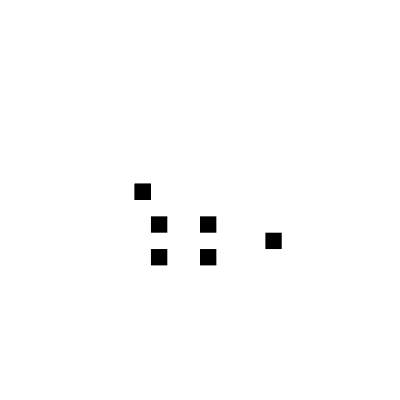

```mathematica
BotMove[pos]
AppendTo[pos,%]
Graphics[Rectangle[#,#+{1,1}]&/@pos,PlotRange->{{-10,10},{-10,10}}]
```